#### Preamble

```mathematica
ClearAll@@{$Context<>"*"}
SetDirectory[NotebookDirectory[]]
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; 
StartScheduledTask[saveTask] (*Saves nb each 15 minutes*) ;

<<"MaTeX`"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Maxima_Minima.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optics_Mie.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/jet_jet-extended.wls"
```

/home/juanathan/Documentos/MSc_Thesis/3-FEM-Calc/2-Supported-TotallyEmbbeded

#### Plots format

```mathematica
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
colors[[1]] = ColorData[3,2];
PrependTo[colors,Black];
```

```mathematica
fs=9;
cdata3 = Table[ColorData[3,i],{i,10}];cdata3[[3]] = Purple;
texStyle:={FontFamily->"Latin Modern Roman",FontSize->fs,Black};
```

```mathematica
graphsOpts:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->215,PlotStyle->colors}
graphsOptsDash:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->215,PlotStyle->Table[Directive[Dashed,colors[[i]]],{i,10}]}
```

```mathematica
graphsOptsPolar:={Mesh->30,BaseStyle->texStyle,PolarAxes->True,FrameStyle->Black,ImageSize->215,
	PlotStyle->Table[Directive[PointSize[.015],colors[[i]]],{i,10}],PolarGridLines->Automatic,Joined->True,GridLinesStyle->Directive[Gray,Opacity[.1]],
	PolarAxesOrigin->{{Left,Up},Automatic}}
graphsOptsPolarDashed:={Mesh->30,BaseStyle->texStyle,PolarAxes->True,FrameStyle->Black,ImageSize->215,
	PlotStyle->Table[Directive[Dashed,PointSize[.015],colors[[i]]],{i,10}],PolarGridLines->Automatic,Joined->True,GridLinesStyle->Directive[Gray,Opacity[.1]],
	PolarAxesOrigin->{{Left,Up},Automatic}}
```

```mathematica
graphsOptsDensity := { BaseStyle -> texStyle, FrameStyle -> Black, PlotRange -> Full,  ColorFunctionScaling -> True, ColorFunction -> JetExtended, Mesh -> None, ImageSize -> 150, PlotRangePadding -> None  }
```

#### Sorting Functions

```mathematica
maxPair[list_,ind_]:= SortBy[list, #[[ind]]&][[-1,{1,ind}]]
makePairs[list_,ind_]:=Map[Table[#[[;;,{1,i}]],{i,ind}]&,list]
```

Efficiencies

### Mie

```mathematica
radius = 12.5;
nNP=JohnsonChristyAuRefSize[#,radius]&;
wlength=Range[400,600,2.5];
max=scaQ=extQ={0,0};

scaFunc[lda_]:=Map[MieScatteringQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];
extFunc[lda_]:=Map[MieExtinctionQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];
```

```mathematica
i=1;
nMat=1.&;
extQ[[i]]=extFunc[wlength];
scaQ[[i]]=scaFunc[wlength];
max[[i]]=FindExtrema[#,wlength[[{1,-1}]],10.,"Maxima"][[1,1]]&/@{extFunc,scaFunc};

i++;
nMat=1.5&;
extQ[[i]]=extFunc[wlength];
scaQ[[i]]=scaFunc[wlength];
max[[i]]=FindExtrema[#,wlength[[{10,-1}]],10.,"Maxima"][[1,1]]&/@{extFunc,scaFunc};

max=Reverse@Transpose[max];
```

```mathematica
mie=MapThread[Show[{ListPlot[#,DataRange->wlength[[{1,-1}]],Joined->True,Filling->{1->{2}},ScalingFunctions->"SignedLog",PlotStyle->{Directive[Thick,Dashed,Green],Directive[Thick,Dashed,Green]}],
ListPlot[Callout[#,ToString[IntegerPart@#[[1]]],Left]&/@#2,ScalingFunctions->"SignedLog"]},PlotRange->All]&,{{extQ-scaQ,scaQ},Reverse@max}]
```

{-Graphics-,-Graphics-}

### Interface

```mathematica
data = Reverse@FileNames["1*","Oblique*"]; data//TableForm
data =Drop[Import[#,"Data"],5]&/@ data;
cases = {2,5,8,11};

maxPointsS =Table[maxPair[data[[#1,10;;]],#2]&[i,j],{i,Length[data]},{j,cases}] ;
dataS =makePairs[data,cases](*pol,angle,Sca/Abs,wlenth, Q*);
maxPointsA =Table[maxPair[data[[#1,10;;]],#2]&[i,j],{i,Length[data]},{j,cases+1}] ;
dataA =makePairs[data,cases+1](*pol,angle,Sca/Abs,wlenth, Q*);
```

Oblique-Supported-Internal/1-Efficiency-s.csv
Oblique-Supported-Internal/1-Efficiency-p.csv

```mathematica
cplots = ResourceFunction["CombinePlots"]
```

```mathematica
plots = {0,0};
plots[[1]] =MapThread[Show[{
ListPlot[#1,PlotMarkers->#4,Mesh->None,Evaluate[#3],Joined->True,ScalingFunctions->"SignedLog"],
ListPlot[Callout[#,ToString[NumberForm[N[#[[1]]],{4,1}]],Below]&/@#,PlotStyle->Directive[PointSize[.02],Blue],ScalingFunctions->"SignedLog"]& @ #2}]&,{dataA,maxPointsA,{graphsOpts,graphsOptsDash},{"●","○"}}];

plots[[2]] = MapThread[Show[{
ListPlot[#1,PlotMarkers->#4,Mesh->None,Evaluate[#3],Joined->True,ScalingFunctions->"SignedLog"],
ListPlot[Callout[#,ToString[NumberForm[N[#[[1]]],{4,1}]],Below]&/@#,PlotStyle->Directive[PointSize[.02],Blue],ScalingFunctions->"SignedLog"]& @ #2}]&,{dataS,maxPointsS,{graphsOpts,graphsOptsDash},{"●","○"}}];

plots = MapThread[Show[{#1,#2},  ScalingFunctions->"SignedLog"]&,{plots,Transpose@@{{mie,mie}}},2]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
(*
plots[[1]] = cplots[#1,#2,"AxesSides"->Automatic,PlotRange->All]& @@ plots[[1]]
plots[[2]] = cplots[#1,#2,"AxesSides"->"TwoY"]& @@ plots[[2]]
*)
```

Near Field Abs

```mathematica
data =  FileNames["2*","Oblique*"];
data//TableForm
data =Drop[Import[#,"Data"],8]&/@ data;
lim = radius*4;
```

Oblique-Supported-Internal/2-Abs-Near-15-p.csv
Oblique-Supported-Internal/2-Abs-Near-15-s.csv
Oblique-Supported-Internal/2-Abs-Near-38-p.csv
Oblique-Supported-Internal/2-Abs-Near-38-s.csv
Oblique-Supported-Internal/2-Abs-Near-42-p.csv
Oblique-Supported-Internal/2-Abs-Near-42-s.csv
Oblique-Supported-Internal/2-Abs-Near-75-p.csv
Oblique-Supported-Internal/2-Abs-Near-75-s.csv

```mathematica
max = Max[data[[;;,;;,4]]] (*To normalize all cases*)
case = -{1,1,1,1,1,1,1,1} (*To place above or below the glass*)

dataX = Table[Select[data[[i]], Abs[#[[2]]]<.001   &],{i,Length[data]}];
dataX = MapThread[#1/. {x_,y_,z_,norm_} -> {x, #2 * z, norm/max} &,{dataX, case}];
dataX = Table[Select[dataX[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataX]}];

dataY = Table[Select[data[[i]], Abs[#[[1]]]<.001   &],{i,Length[data]}];
dataY = MapThread[#/. {x_,y_,z_,norm_} -> {y, #2 * z, norm/max} &, {dataY, case}];
dataY = Table[Select[dataY[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataY]}];
```

9.20475

{-1,-1,-1,-1,-1,-1,-1,-1}

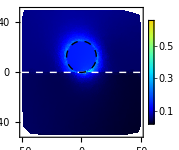
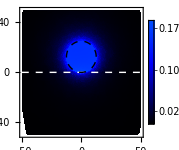
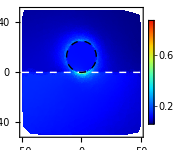
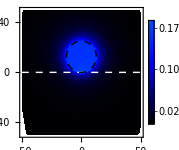
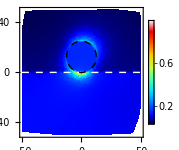
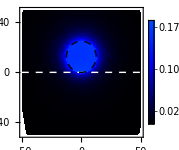
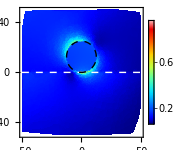
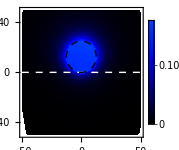

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
system = {White,Dashed, Line[{{-lim,0},{lim,0}}],Black, Circle[{0,radius*#},radius]}&/@{1,1,1,1,1,1,1,1};
tf = False;

plotsX = MapThread[ListDensityPlot[#1,ColorFunctionScaling->tf,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataX,system}]
plotsY = MapThread[ListDensityPlot[#1,ColorFunctionScaling->tf,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataY,system}]
```

Near Field Sca

```mathematica
data =  FileNames["3*","Oblique*"];
data//TableForm
data =Drop[Import[#,"Data"],8]&/@ data;
lim = radius*4;
```

Oblique-Supported-Internal/3-Sca-Near-15.csv
Oblique-Supported-Internal/3-Sca-Near-15-p.csv
Oblique-Supported-Internal/3-Sca-Near-38-p.csv
Oblique-Supported-Internal/3-Sca-Near-38-s.csv
Oblique-Supported-Internal/3-Sca-Near-42-p.csv
Oblique-Supported-Internal/3-Sca-Near-42-s.csv
Oblique-Supported-Internal/3-Sca-Near-75-p.csv
Oblique-Supported-Internal/3-Sca-Near-75-s.csv

```mathematica
max = Max[data[[;;,;;,4]]] (*To normalize all cases*)
case = -{1,1,1,1,1,1,1,1} (*To place above or below the glass*)

dataX = Table[Select[data[[i]], Abs[#[[2]]]<.001   &],{i,Length[data]}];
dataX = MapThread[#1/. {x_,y_,z_,norm_} -> {x, #2 * z, norm/max} &,{dataX, case}];
dataX = Table[Select[dataX[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataX]}];

dataY = Table[Select[data[[i]], Abs[#[[1]]]<.001   &],{i,Length[data]}];
dataY = MapThread[#/. {x_,y_,z_,norm_} -> {y, #2 * z, norm/max} &, {dataY, case}];
dataY = Table[Select[dataY[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataY]}];
```

12.2363

{-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
system = {White,Dashed, Line[{{-lim,0},{lim,0}}],Black, Circle[{0,radius*#},radius]}&/@{1,1,1,1,1,1,1,1};
tf = False;

plotsX = MapThread[ListDensityPlot[#1,ColorFunctionScaling->tf,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataX,system}]
plotsY = MapThread[ListDensityPlot[#1,ColorFunctionScaling->tf,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataY,system}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Far Field (Normal X, Abs)

```mathematica
data =  FileNames["4*","Oblique*"]; data//TableForm
data =Drop[Import[#,"Data"],8]&/@ data;
data = Map[Partition[#,51]&,data]; (*Separete eat wlength value*)
```

Oblique-Supported-Internal/4-Far-NormalX-Abs-p.csv
Oblique-Supported-Internal/4-Far-NormalX-Abs-s.csv

```mathematica
thTiks=Table[{i*Pi/180.,
Which[i≤90,(90-i)Degree,
i<= 180,""(*Mod[i,90]*),
i< 270,(90-Mod[i,90])Degree,
True, Mod[i,90]Degree
]},{i,0,360,15}];

arrows ={#3,Arrow[-#2*{{Cos[#1],Sin[#1]},.025{Cos[#1],Sin[#1]}}]}&;
```

```mathematica
ClearAll[arrowList]

max = Max[#[[;;,;;,2]]]&/@data;
caseDir = 90-{15, 38, 42,75}; (*To place the incoming wave direction*)
arrowList[max_] := MapThread[arrows[#1 Degree,max*1.1,#2]&, {caseDir,colors[[;;4]]}]

MapThread[
ListPolarPlot[#1/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->#2*1.65,
PolarAxesOrigin->{{Left,Up},#2},
Evaluate[graphsOptsPolar],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->{LightBlue,Disk[{0,0},#2*1.65,{0,-Pi}],LightYellow,Disk[{0,#2}/3.5,#2/3.5]},
Epilog->arrowList[#2]
]&,
{data,max}]
```

{-Graphics-,-Graphics-}

Far Field (Normal Y, Abs)

```mathematica
data =  FileNames["5*","Oblique*"]; data//TableForm
data =Drop[Import[#,"Data"],8]&/@ data;
data = Map[Partition[#,51]&,data]; (*Separete eat wlength value*)
```

Oblique-Supported-Internal/5-Far-NormalY-Abs-p.csv
Oblique-Supported-Internal/5-Far-NormalY-Abs-s.csv

```mathematica
thTiks=Table[{i*Pi/180.,
Which[i≤90,(90-i)Degree,
i<= 180,""(*Mod[i,90]*),
i< 270,(90-Mod[i,90])Degree,
True, Mod[i,90]Degree
]},{i,0,360,15}];

arrows ={#3,Arrow[-#2*{{Cos[#1],Sin[#1]},.025{Cos[#1],Sin[#1]}}]}&;
```

```mathematica
ClearAll[arrowList]

max = Max[#[[;;,;;,2]]]&/@data;
caseDir = 90-{15, 38, 42,75}; (*To place the incoming wave direction*)
arrowList[max_] := MapThread[arrows[#1 Degree,max*1.1,#2]&, {caseDir,colors[[;;4]]}]

MapThread[
ListPolarPlot[#1/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->#2*1.65,
PolarAxesOrigin->{{Left,Up},#2},
Evaluate[graphsOptsPolar],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->{LightBlue,Disk[{0,0},#2*1.65,{0,-Pi}],LightYellow,Disk[{0,#2}/3.5,#2/3.5]},
Epilog->arrowList[#2]
]&,
{data,max}]
```

{-Graphics-,-Graphics-}

Far Field (Normal X, Sca)

```mathematica
data =  FileNames["6*","Oblique*"]; data//TableForm
data =Drop[Import[#,"Data"],8]&/@ data;
data = Map[Partition[#,51]&,data]; (*Separete eat wlength value*)
```

Oblique-Supported-Internal/6-Far-NormalX-Sca-p.csv
Oblique-Supported-Internal/6-Far-NormalX-Sca-s.csv

```mathematica
thTiks=Table[{i*Pi/180.,
Which[i≤90,(90-i)Degree,
i<= 180,""(*Mod[i,90]*),
i< 270,(90-Mod[i,90])Degree,
True, Mod[i,90]Degree
]},{i,0,360,15}];

arrows ={#3,Arrow[-#2*{{Cos[#1],Sin[#1]},.025{Cos[#1],Sin[#1]}}]}&;
```

```mathematica
ClearAll[arrowList]

max = Max[#[[;;,;;,2]]]&/@data;
caseDir = 90-{15, 38, 42,75}; (*To place the incoming wave direction*)
arrowList[max_] := MapThread[arrows[#1 Degree,max*1.1,#2]&, {caseDir,colors[[;;4]]}]

MapThread[
ListPolarPlot[#1/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->#2*1.65,
PolarAxesOrigin->{{Left,Up},#2},
Evaluate[graphsOptsPolar],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->{LightBlue,Disk[{0,0},#2*1.65,{0,-Pi}],LightYellow,Disk[{0,#2}/3.5,#2/3.5]},
Epilog->arrowList[#2]
]&,
{data,max}]
```

{-Graphics-,-Graphics-}

Far Field (Normal Y, Sca)

```mathematica
data =  FileNames["7*","Oblique*"]; data//TableForm
data =Drop[Import[#,"Data"],8]&/@ data;
data = Map[Partition[#,51]&,data]; (*Separete eat wlength value*)
```

Oblique-Supported-Internal/7-Far-NormalY-Sca-p.csv
Oblique-Supported-Internal/7-Far-NormalY-Sca-s.csv

```mathematica
thTiks=Table[{i*Pi/180.,
Which[i≤90,(90-i)Degree,
i<= 180,""(*Mod[i,90]*),
i< 270,(90-Mod[i,90])Degree,
True, Mod[i,90]Degree
]},{i,0,360,15}];

arrows ={#3,Arrow[-#2*{{Cos[#1],Sin[#1]},.025{Cos[#1],Sin[#1]}}]}&;
```

```mathematica
ClearAll[arrowList]

max = Max[#[[;;,;;,2]]]&/@data;
caseDir = 90-{15, 38, 42,75}; (*To place the incoming wave direction*)
arrowList[max_] := MapThread[arrows[#1 Degree,max*1.1,#2]&, {caseDir,colors[[;;4]]}]

MapThread[
ListPolarPlot[#1/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->#2*1.65,
PolarAxesOrigin->{{Left,Up},#2},
Evaluate[graphsOptsPolar],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->{LightBlue,Disk[{0,0},#2*1.65,{0,-Pi}],LightYellow,Disk[{0,#2}/3.5,#2/3.5]},
Epilog->arrowList[#2]
]&,
{data,max}]
```

{-Graphics-,-Graphics-}